```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["Pegasus`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Pegasus.m"}]] (* Load Pegasus strategies package from current directory *)

(* Drawing primitive *)
DrawPlanarProb[prob_List, invariant_] := Module[{},
    { init, { f, {x, y}, H }, safe } = prob;
    {x1min, x1max} = {-6, 6};
    {x2min, x2max} = {-6, 6};
    
    Show[
      RegionPlot[Not[safe], {x, x1min, x1max}, {y, x2min, x2max}, PlotStyle -> Red, FrameLabel -> {x, y}, FrameTicks -> None, LabelStyle -> Directive[Large]], (* Plot unsafe states in red *)
      RegionPlot[init, {x, x1min, x1max}, {y, x2min, x2max}, PlotStyle -> Green], (* Plot initial states in green *)
      RegionPlot[Apply[And, invariant], {x, x1min, x1max}, {y, x2min, x2max}], (* Plot invariant *)
      StreamPlot[f, {x, x1min, x1max}, {y, x2min, x2max}, StreamStyle -> Darker[Gray]] (* Plot vector field *)
      ]
    ]
```

### One-dimensional system tests

```mathematica
OneDimRhs1={
x≤-2, 
{{x^2+x-1},{x}, True},
  x<4
};
OneDimRhsInv1=InvGen[OneDimRhs1]
```

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Precondition is not an invariant. Proceeding.

Relaxed invariant is no longer invariant. Sorry.

{{True},False}

### Constant right-hand side system tests

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Precondition is not an invariant. Proceeding.

CONSTANT STRATEGY

4 x+x^2-4 y+y^2≤-23/3||(x+2 y≥2&&24 x+4 x^2-12 y-4 x y+y^2≤-103/3)||(x+2 y≥2&&-16 x+4 x^2+8 y-4 x y+y^2≤-11)||(x>0&&-4 x+x^2+y^2≤-3)

Relaxed invariant is still ok. Proceeding

Generated invariant implies postcondition. Returning.

{{(x+2 y≥2&&(103+3 (4 x (6+x)-4 x y+y^2)≤36 y||11+4 x^2+y (8+y)≤4 x (4+y)))||3+x^2+y^2≤4 x||23+3 x (4+x)+3 (-4+y) y≤0},True}

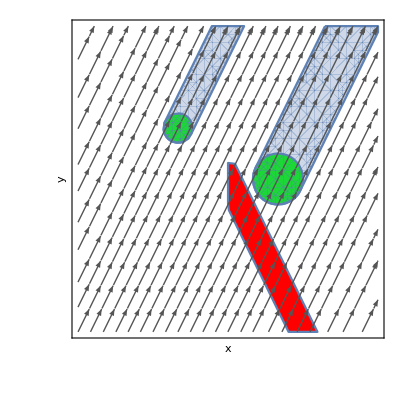

```mathematica
constantRhs1={
(x-2)^2+y^2≤1 || (x+2)^2+(y-2)^2≤1/3, 
{{1, 2},{x,y}, True},
  (-1/2y-x)^2≥1/3 ||x<=0
};
constantRhsInv1=Pegasus[constantRhs1]
DrawPlanarProb[constantRhs1, constantRhsInv1//First]
```

### Two-dimensional linear system tests

```mathematica
planarLin1={
x≤1 && x==0 && y==1,
{{x'=y,y'=-x},{x,y}, True},
x≤1
};
 planarLinInv1=Pegasus[planarLin1]
DrawPlanarProb[planarLin1, planarLinInv1//First];
```

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Precondition is not an invariant. Proceeding.

GENERAL LINEAR STRATEGY

Trying first integrals first

{0,1-x^2-y^2}

DC on True

DC on 1-x^2-y^2==0

DW

Relaxed invariant is still ok. Proceeding

Generated invariant implies postcondition. Returning.

{{True,x^2+y^2==1},True}

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Precondition is not an invariant. Proceeding.

GENERAL LINEAR STRATEGY

Trying first integrals first

Solve::svars: Equations may not give solutions for all "solve" variables.

{-185/6+x^2+4 y^2,-82/7+x^2+4 y^2,-6+x^2+4 y^2,-53/22+x^2+4 y^2}

DC on -185/6+x^2+4 y^2<0

DC on -53/22+x^2+4 y^2>0

DW

Relaxed invariant is still ok. Proceeding

Generated invariant implies postcondition. Returning.

{{x^2+4 y^2<185/6,x^2+4 y^2>53/22},True}

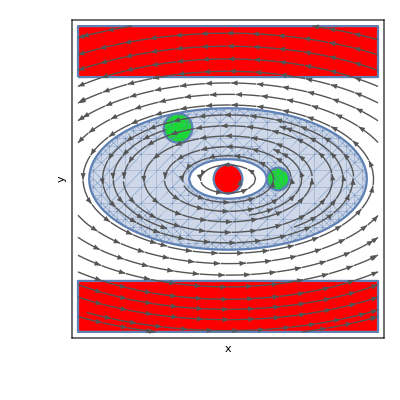

```mathematica
planarLin2={
(x-2)^2+y^2≤1/5 || (x+2)^2+(y-2)^2≤1/3, 
{{-4y, x},{x,y}, True}, 
 y≤4 &&y≥-4 &&Not[x^2+y^2≤1/3]
};
planarLinInv2=Pegasus[planarLin2]
DrawPlanarProb[planarLin2, planarLinInv2//First]
```

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Precondition is not an invariant. Proceeding.

GENERAL LINEAR STRATEGY

Trying first integrals first

{}

{}

{1/2 (-1-√13) x+y,1/2 (-1+√13) x+y}

{1/2 (-1-√13) x+y,1/2 (-1+√13) x+y}

{1/2 (-1-√13) x+y,-(2 (17+5 √13))/(7+√13)-(√(2/3 (185+47 √13)))/(7+√13)+1/2 (-1-√13) x+y,-(2 (17+5 √13))/(7+√13)+(√(2/3 (185+47 √13)))/(7+√13)+1/2 (-1-√13) x+y,1/2 (-1+√13) x+y,-(√(2/3 (185-47 √13)))/(7-√13)-(2 (-17+5 √13))/(-7+√13)+1/2 (-1+√13) x+y,(√(2/3 (185-47 √13)))/(7-√13)-(2 (-17+5 √13))/(-7+√13)+1/2 (-1+√13) x+y}

DC on 1/2 (-1-√13) x+y>0

DW

{}

{1/2 (-1-√13) x+y,1/2 (-1+√13) x+y}

{1/2 (-1-√13) x+y,1/2 (-1+√13) x+y}

{1/2 (-1-√13) x+y,(4 (5+2 √13))/(7+√13)-(√(2/5 (185+47 √13)))/(7+√13)+1/2 (-1-√13) x+y,(4 (5+2 √13))/(7+√13)+(√(2/5 (185+47 √13)))/(7+√13)+1/2 (-1-√13) x+y,1/2 (-1+√13) x+y,-(√(2/5 (185-47 √13)))/(7-√13)+(4 (-5+2 √13))/(-7+√13)+1/2 (-1+√13) x+y,(√(2/5 (185-47 √13)))/(7-√13)+(4 (-5+2 √13))/(-7+√13)+1/2 (-1+√13) x+y}

DC on 1/2 (-1-√13) x+y<0

DC on (4 (5+2 √13))/(7+√13)-(√(2/5 (185+47 √13)))/(7+√13)+1/2 (-1-√13) x+y≤0

DC on 1/2 (-1+√13) x+y>0

DW

Relaxed invariant is still ok. Proceeding

Generated invariant implies postcondition. Returning.

{{2 y>x+√13 x||(5 (20+8 √13+(7+√13) y)≤√(1850+470 √13)+10 (5+2 √13) x&&√13 x+2 y>x)},True}

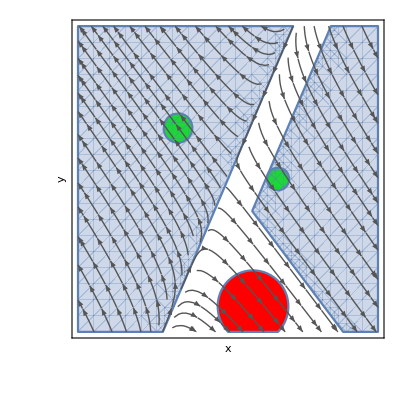

```mathematica
planarLin3={
(x-2)^2+y^2≤1/5 || (x+2)^2+(y-2)^2≤1/3,
 {{2x-y, -3*x+y},{x,y}, True},  
(x-1)^2+(y+5)^2≥2
};
planarLinInv3=Pegasus[planarLin3]
DrawPlanarProb[planarLin3, planarLinInv3//First]
```

```mathematica
planarLin4={
(x-2)^2+y^2≤1/5 || (x+2)^2+(y-2)^2≤1/3, 
{{-2x+y, x-3*y},{x,y}, True}, 
 Not[(y≥1)&&(x≤1 && x≥0) || x^2+(y+3)^2≤1 || (x+6)^2+(y-1)^2≤1/3]
};
planarLinInv4=Pegasus[planarLin4]
DrawPlanarProb[planarLin4, planarLinInv4//First]
```

#### Higher-dimensional linear system tests

#### Planar non-linear system tests

{x^2≤1/2&&y^2≤1/3,{{y-x^7 (-10+x^4+2 y^2),-x^3-3 y^5 (-10+x^4+2 y^2)},{x,y},True},(-2+x)^2+(-3+y)^2>1/4}

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Precondition is not an invariant. Proceeding.

QualitativeAbstraction`SummandFactors

{y,x,-10+x^4+2 y^2}

Invariant

{-10+x^4+2 y^2<0,{-10+x^4+2 y^2<0}}

{x^4+2 y^2<10,{x^4+2 y^2<10}}

Generated invariant implies postcondition. Returning.

{x^4+2 y^2<10,True}

ImplicitRegion::bcond: x^4+2 y^2&&10 should be a Boolean combination of equations, inequalities, and Element statements.

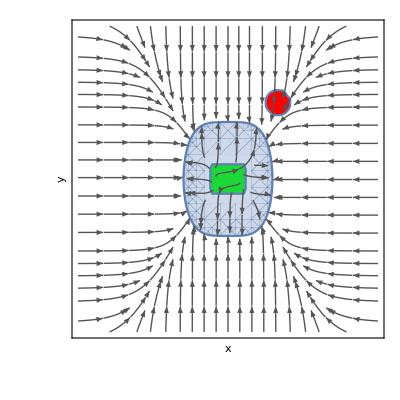

```mathematica
MIT={x^2≤1/2&& y^2≤1/3,{{y-x^7*(x^4+2*y^2-10),-x^3-3*(y^5)*(x^4+2*y^2-10)},{x,y},True},((-2+x)^2+(-3+y)^2>1/4)}

MITInv=Pegasus`InvGen[MIT]
DrawPlanarProb[MIT, MITInv//First]
```

{0.5≤x&&x≤0.7&&0≤y&&y≤0.3,{{-x+x y,-y},{x,y},True},!(-0.8≥x&&x≥-1&&-0.7≥y&&y≥-1)}

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Precondition is not an invariant. Proceeding.

QualitativeAbstraction`SummandFactors

{x,y}

Invariant

{x>0,{x>0}}

{x>0,{x>0}}

Generated invariant implies postcondition. Returning.

{x>0,{x>0}}

ImplicitRegion::bcond: x&&0 should be a Boolean combination of equations, inequalities, and Element statements.

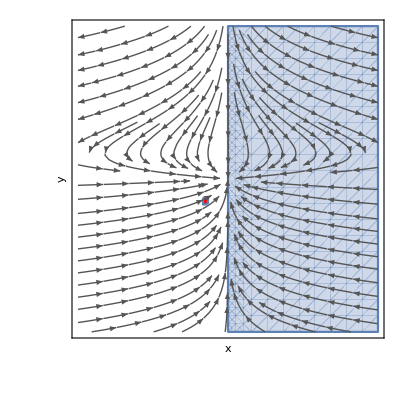

```mathematica
Ahmadi={0.5≤x&& x≤0.7&& 0≤y&& y≤0.3,{{-x+x*y,-y},{x,y},True},Not[(-0.8≥x&& x≥-1&&-0.7≥y&& y≥-1)]}
AhmadiInv=Pegasus`InvGen[Ahmadi]//First
DrawPlanarProb[Ahmadi, AhmadiInv//First]
```

{x>-1/2&&x<-1/3&&y<0&&y≥-1/2,{{x (1-x^2-y^2)+y ((-1+x^2)^2+y^2),y (1-x^2-y^2)-y ((-1+x^2)^2+y^2)},{x,y},True},x<0}

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Precondition is not an invariant. Proceeding.

QualitativeAbstraction`SummandFactors

{x,-1+x^2+y^2,y,1-2 x^2+x^4+y^2}

Invariant

{y<0&&x<0,{y<0,x<0}}

{y<0&&x<0,{y<0,x<0}}

Generated invariant implies postcondition. Returning.

{y<0&&x<0,{y<0,x<0}}

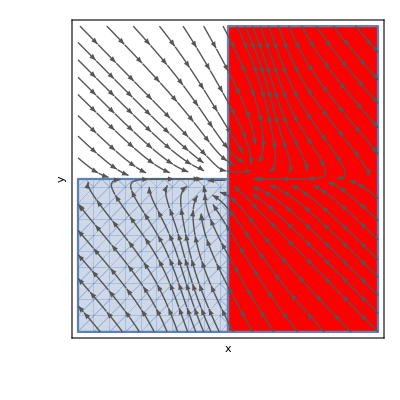

```mathematica
Dumortier19a={x>-1/2&& x<-1/3&& y<0&& y≥-1/2,
{{x*(1-x^2-y^2)+y*((-1+x^2)^2+y^2),y*(1-x^2-y^2)-y*((-1+x^2)^2+y^2)},{x,y},True},
Not[(x≥0)]}

(* This problem isn't difficult, but fails because of the way invariants are extracted from the algebraic decomposition, i.e. only considering non-strict inequalities *)

DumortierInv=Pegasus`InvGen[Dumortier19a]//First
DrawPlanarProb[Dumortier19a, DumortierInv//First]
```

{x^2+(-2+y)^2<1/24,{{-x+2 x^2 y,-y},{x,y},True},!(x≤-2||y≤-1)}

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Precondition is not an invariant. Proceeding.

QualitativeAbstraction`SummandFactors

{x,y}

Invariant

{y>0,{y>0}}

{y>0,{y>0}}

Generated invariant does not imply postcondition. Bad luck; returning what I could find.

{y>0,{y>0}}

ImplicitRegion::bcond: y&&0 should be a Boolean combination of equations, inequalities, and Element statements.

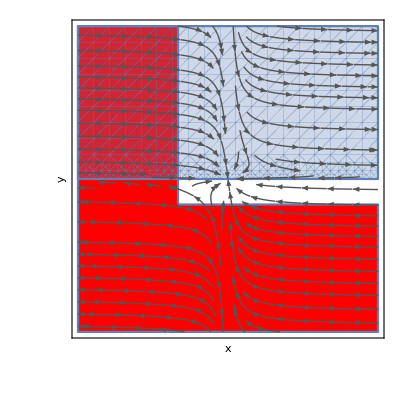

```mathematica
Forsman={x^2+(-2+y)^2<1/24,
{{-x+2*x^2*y,-y},{x,y},True},
Not[(x≤-2||y≤-1)]}
ForsmanInv=Pegasus`InvGen[Forsman]//First
DrawPlanarProb[Forsman, ForsmanInv//First]
```

{-1/5000+(1/20+x)^2+(3/200+y)^2≤0,{{-(3 x^2)/2-x^3/2-y,3 x-y},{x,y},True},49/100+x+x^2+y+y^2>0}

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Precondition is not an invariant. Proceeding.

SummandFactors

{x,y}

Invariant

{True,{}}

{True,{}}

Generated invariant does not imply postcondition. Bad luck; returning what I could find.

DarbouxPolynomials

Generated Darboux polynomials:

{}

{}

Invariant

{True,{}}

{True,{}}

Generated invariant does not imply postcondition. Bad luck; returning what I could find.

SOSBarrier

OpenMATLAB::wspo: The MATLAB workspace is already open.

{-2621/25000+x/250000+(1383 x^2)/1000-(77759 x^3)/1000000+(1517 x^4)/12500-(5401 x y)/12500+(81807 x^2 y)/100000-(19301 x^3 y)/1000000+(6589 y^2)/12500-(11503 x y^2)/100000+(14523 x^2 y^2)/100000+(9619 y^3)/50000+(x y^3)/125000+(5091 y^4)/200000}

Invariant

{-2621/25000+x/250000+(1383 x^2)/1000-(77759 x^3)/1000000+(1517 x^4)/12500-(5401 x y)/12500+(81807 x^2 y)/100000-(19301 x^3 y)/1000000+(6589 y^2)/12500-(11503 x y^2)/100000+(14523 x^2 y^2)/100000+(9619 y^3)/50000+(x y^3)/125000+(5091 y^4)/200000<0,{-2621/25000+x/250000+(1383 x^2)/1000-(77759 x^3)/1000000+(1517 x^4)/12500-(5401 x y)/12500+(81807 x^2 y)/100000-(19301 x^3 y)/1000000+(6589 y^2)/12500-(11503 x y^2)/100000+(14523 x^2 y^2)/100000+(9619 y^3)/50000+(x y^3)/125000+(5091 y^4)/200000<0}}

{121360 x^4+30 x^2 (46100+y (27269+4841 y))+5 y^2 (105424+y (38476+5091 y))+2 x (2+y (-216040+y (-57515+4 y)))<104840+x^3 (77759+19301 y),{121360 x^4+30 x^2 (46100+y (27269+4841 y))+5 y^2 (105424+y (38476+5091 y))+2 x (2+y (-216040+y (-57515+4 y)))<104840+x^3 (77759+19301 y)}}

Generated invariant implies postcondition. Returning.

{121360 x^4+30 x^2 (46100+y (27269+4841 y))+5 y^2 (105424+y (38476+5091 y))+2 x (2+y (-216040+y (-57515+4 y)))<104840+x^3 (77759+19301 y),{121360 x^4+30 x^2 (46100+y (27269+4841 y))+5 y^2 (105424+y (38476+5091 y))+2 x (2+y (-216040+y (-57515+4 y)))<104840+x^3 (77759+19301 y)}}

ImplicitRegion::bcond: 121360 x^4+30 x^2 (46100+y (27269+4841 y))+5 y^2 (105424+y (38476+5091 y))+2 x (2+y (-216040+y Plus[«2»]))&&104840+x^3 (77759+19301 y) should be a Boolean combination of equations, inequalities, and Element statements.

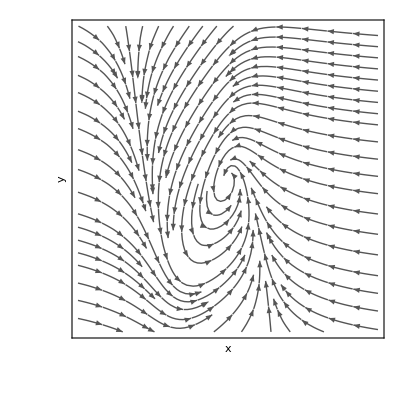

```mathematica
JetEngine={ -1/5000+(1/20+x)^2+(3/200+y)^2≤0,{{(-3*x^2)/2-x^3/2-y,3*x-y},{x,y},True}, Not[(49/100+x+x^2+y+y^2≤0)]}
JetEngineInv=Pegasus`InvGen[JetEngine]//First
DrawPlanarProb[JetEngine, JetEngineInv//First]
```

{(2+x)^2+(-1+y)^2≤1/4,{{x^2+2 x y+3 y^2,2 y (2 x+y)},{x,y},True},x≤0}

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Precondition is not an invariant. Proceeding.

BASIC QUALITATIVE STRATEGY (DWC)

DC on y>0

No more cuts ...

DC on x^2+2 x y+3 y^2>0

No more cuts ...

Generated Darboux polynomials:

{x-y,x+y,y}

DC on x-y<0

DC on y>0

DC on x+y<0

DW

Basic qualitative strategy success!

Relaxed invariant is still ok. Proceeding

Generated invariant implies postcondition. Returning.

{{x<y,y>0,x+y<0},True}

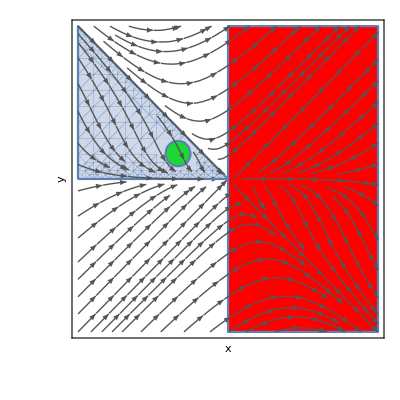

```mathematica
CollinGoriely={(2+x)^2+(-1+y)^2≤1/4,{{x^2+2*x*y+3*y^2,2*y*(2*x+y)},{x,y},True},Not[(x>0)]}
CollinGorielyInv=Pegasus[CollinGoriely]
DrawPlanarProb[CollinGoriely, CollinGorielyInv//First]
```

{(2+x)^2+(-1+y)^2≤1/4,{{x^2+2 x y+3 y^2,2 y (2 x+y)},{x,y},True},x≤0}

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Precondition is not an invariant. Proceeding.

BASIC QUALITATIVE STRATEGY (DWC)

DC on x<0

DC on x^2+y^2>0

No more cuts ...

No more cuts ...

Generated Darboux polynomials:

{x,x+y}

DC on x<0

DC on x+y>0

No more cuts ...

DC on x<0

DC on x+x^2 y+y^3>0

DW

Basic qualitative strategy success!

Relaxed invariant is still ok. Proceeding

Generated invariant implies postcondition. Returning.

{{x<0,x+x^2 y+y^3>0},True}

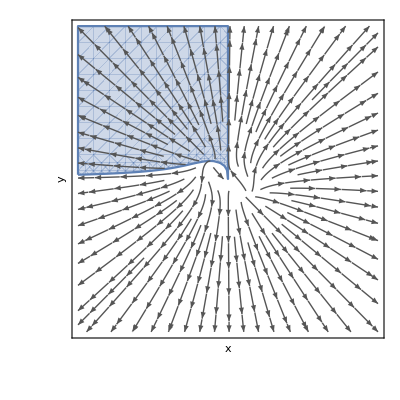

```mathematica
planarNonLin1={
x>-4/5&&x<-1/3&&y<3/2&&y≥1, 
{{-x+a*x(x^2+y^2),x+a*y(x^2+y^2)}/.{a->1},{x,y}, True},
x≥-1/3||y<0||2 y≥1||x≤-4/5
};


 planarNonLinInv1=Pegasus[planarNonLin1]
DrawPlanarProb[planarNonLin1, planarNonLinInv1//First]
```

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Precondition is not an invariant. Proceeding.

BASIC QUALITATIVE STRATEGY (DWC)

DC on -1+y^2≤0

No more cuts ...

$Aborted

First::normal: Nonatomic expression expected at position 1 in First[planarNonLinInv2].

ImplicitRegion::bcond: planarNonLinInv2 should be a Boolean combination of equations, inequalities, and Element statements.

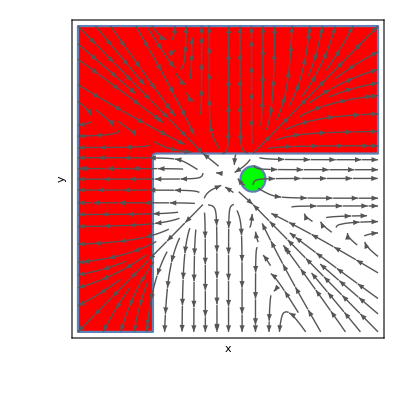

```mathematica
planarNonLin2={
(x-1)^2+y^2<1/4, 
{{(-1+x^2) (-(-2+√5)^2+x^2) (x+√5*y),(√5 x+y) (-1+y^2) (-(-2+√5)^2+y^2)},{x,y}, True},
 y<1 && x>-3
};
planarNonLinInv2=Pegasus[planarNonLin2]
DrawPlanarProb[planarNonLin2,  planarNonLinInv2//First]
```

#### Higher-dimensional non-linear system tests

```mathematica
Linear`FirstIntegralMethod[(x-2)^2+y^2≤1/5 || (x+2)^2+(y-2)^2≤1/3,Not[(y≥1)&&(x≤1 && x≥0) || x^2+(y+3)^2≤1 || (x+6)^2+(y-1)^2≤1/3],
 {{-2x+y, x-3*y},{x,y}, True}, RationalsOnly->True, RationalPrecision->3]
```

```mathematica
FirstIntegralGen`FindFirstIntegrals[2, {x,y}, {-2x+y, x-3*y}]
```